```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"clipped-captures-bloc-calibration","center-finder_centroid_log.csv"}],"Table","FieldSeparators"->";"]
X=Partition[data[[All,3]],5]
Y=data[[All,4]]
```

{{0,/home/benjamin/Desktop/captures-bloc-calibration-cropped//00000000-0.png,1844.31,113.037},{1,/home/benjamin/Desktop/captures-bloc-calibration-cropped//00000000-1.png,1844.28,113.039},{2,/home/benjamin/Desktop/captures-bloc-calibration-cropped//00000000-2.png,1844.29,113.023},42495,{42498,/home/benjamin/Desktop/captures-bloc-calibration-cropped//00849900-3.png,959.621,98.5093},{42499,/home/benjamin/Desktop/captures-bloc-calibration-cropped//00849900-4.png,959.508,98.3821}}
 |  |  |  |

{{1844.31,1844.28,1844.29,1844.32,1844.28},{1843.47,1843.46,1843.46,1843.47,1843.46},{1842.73,1842.74,1842.74,1842.74,1842.73},8494,{959.568,959.494,959.52,958.403,959.469},{960.564,959.54,959.461,959.574,960.441},{959.575,959.551,959.555,959.621,959.508}}
 |  |  |  |

{113.037,113.039,113.023,113.024,113.042,112.572,112.557,112.57,112.568,112.579,112.397,112.389,112.404,112.399,112.409,112.291,42468,98.7033,98.5107,98.7079,98.3868,98.5093,98.4747,98.5923,98.515,98.5675,98.6696,98.7894,98.7541,98.3678,98.5328,98.5093,98.3821}
 |  |  |  |

-Graphics-

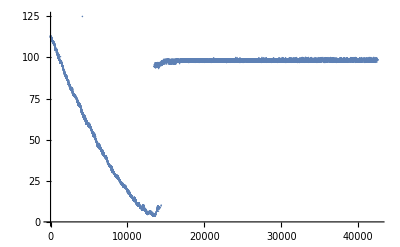

```mathematica
BoxWhiskerChart[X]
ListPlot[Y]
```